Model-independent inference of laser intensity

T. G. Blackburn, E. Gerstmayr, S. P. D. Mangles, and M. Marklund,
PHYSICAL REVIEW ACCELERATORS AND BEAMS 23, 064001 (2020)

Notebook: Óscar Amaro,  2021 + June 2022,  @ GoLP-EPP

Abstract
“measurement of the variances of this profile in the planes parallel and perpendicular to the laser polarization, and the mean initial and final energies of the electron beam, allows the intensity of the laser pulse to be inferred in a way that is independent of the model of the electron dynamics”

## Figure 1

```mathematica
Clear[σpll,σprp,γi,γf,a0,f2,f4,R,ω0,ω0eV,τ]

m=0.511 10^6;(*[eV]*)
α=1/137;(*[]*)
f2=ω0 τ Sqrt[π/(4Log[2])];
f4=f2/Sqrt[2];

(*equation 1*)
σprp=Sqrt[5/(8γi γf)+δ^2];
(*equation 2*)
σpll=Sqrt[a0^2/(4γi γf)f4/f2+σprp^2];

λμm=0.8;(*[μm]*)

ω0=2π  3 10^8/(λμm 10^-6);(*[s-1]*)
ω0eV=ω0 1.05 10^-34 /(9.11 10^-31 (3 10^8)^2) m; (*[eV]*)
τ=40 10^-15;(*[s]*)

δ=2 10^-3;(*[rad]*)

(*equation 3*)
γf=γi/(1+R γi);
R=(2α a0^2 ω0eV)/(3m)f2;

(* plot *)
GraphicsRow[{LogPlot[{10^3 σpll/.{γi->500 10^6 /m},10^3 σpll/.{γi->1000 10^6 /m}},{a0,0,53},AspectRatio->1,ImageSize->200,PlotStyle->{Orange,Blue},Frame->True,FrameLabel->{"a0","σ||[mrad]"},PlotLegends->{"500MeV","1GeV"}],LogPlot[{10^3 σprp/.{γi->500 10^6 /m},10^3 σprp/.{γi->1000 10^6 /m}},{a0,0,53},AspectRatio->1,ImageSize->200,PlotStyle->{Orange,Blue},Frame->True,FrameLabel->{"a0","σ⊥[mrad]"},PlotLegends->{"500MeV","1GeV"}]},ImageSize->700]
```

-Graphics-

## Figure 2

```mathematica
Clear[σpll,σprp,γi,γf,a0,f2,f4,R,ω0,ω0eV,τ]

m=0.511 10^6;(*[eV]*)
α=1/137;(*[]*)
f2=ω0 τ Sqrt[π/(4Log[2])];
f4=f2/Sqrt[2];

(*equation 1*)
σprp=Sqrt[5/(8γi γf)+δ^2];
(*equation 2*)
σpll=Sqrt[a0^2/(4γi γf)f4/f2+σprp^2];

(*equation 1 noRR*)
σprpnoRR=Sqrt[5/(8γi γi)+δ^2];
(*equation 2 noRR*)
σpllnoRR=Sqrt[a0^2/(4γi γi)f4/f2+σprp^2];

λμm=0.8;(*[μm]*)

ω0=2π  3 10^8/(λμm 10^-6);(*[s-1]*)
ω0eV=ω0 1.05 10^-34 /(9.11 10^-31 (3 10^8)^2) m; (*[eV]*)
τ=40 10^-15;(*[s]*)

δ=2 10^-3;(*[rad]*)

(*equation 3*)
γf=γi/(1+R γi);
R=(2α a0^2 ω0eV)/(3m)f2;
a0=20;

(* plot *)
GraphicsRow[{Plot[{10^3 σpll/.{γi->500 10^6 /m},10^3 σpll/.{γi->1000 10^6 /m},10^3 σpllnoRR/.{γi->500 10^6 /m},10^3 σpllnoRR/.{γi->1000 10^6 /m}},{Δ,0,0.2},AspectRatio->1,ImageSize->200,PlotStyle->{Directive[Orange],Directive[Blue],Directive[Orange,Dashed],Directive[Blue,Dashed]},Frame->True,FrameLabel->{"Δ","σ||[mrad]"},PlotLegends->{"500MeV","1GeV"},PlotRange->{0,15}],LogPlot[{10^3 σprp/.{γi->500 10^6 /m},10^3 σprp/.{γi->1000 10^6 /m},10^3 σprpnoRR/.{γi->500 10^6 /m},10^3 σprpnoRR/.{γi->1000 10^6 /m}},{Δ,0,0.2},AspectRatio->1,ImageSize->200,PlotStyle->{Directive[Orange],Directive[Blue],Directive[Orange,Dashed],Directive[Blue,Dashed]},Frame->True,FrameLabel->{"Δ","σ⊥[mrad]"},PlotLegends->{"500MeV","1GeV"},PlotRange->{1.9,2.4}]},ImageSize->700]
```

-Graphics-

## Equation 6: infered a0

```mathematica
Clear[a,a0,n,a2,a4,x,y,W0,xb,ξ,P,Q,nnorm]

(* laser profile at z=0 *)
a=a0 Exp[-(x^2+y^2)/W0^2];

(* density profile at z=0 *)
n=Exp[-0.5((x-xb)^2+y^2)/rb^2];

nnorm=2 π rb^2;

(* <a^2> *)
a2=(Integrate[ a^2 n,{x,-∞,∞},{y,-∞,∞}]/nnorm)//Normal

(* <a^4> *)
a4=(Integrate[ a^4 n,{x,-∞,∞},{y,-∞,∞}]/nnorm)//Normal

(* <a^4>/<a^2> *)
a42=Refine[Refine[a4/a2,{W0>0,rb>0}]//Simplify,{W0>0,rb>0}]//Factor

Clear[P,Q,ξ,ρ]
P=1+4ρ^2;
Q=1+8ρ^2;
ξ=xb/W0;
ρ=rb/W0;
(* equation 6 *)
a0inf2=a0^2 (P/Q) Exp[-2ξ^2/(P Q)]

(* the two expressions are equivalent, confirming equation 6 *)
(a0inf2-a42 )//N//Simplify
```

(0.282095 a0^2 ⅇ^(-(0.5 xb^2)/(1. rb^2+0.25 W0^2)))/(rb^2 √(0.159155/rb^2+0.63662/W0^2) √(0.5/rb^2+2./W0^2))

(0.282095 a0^4 ⅇ^(-(0.5 xb^2)/(1. rb^2+0.125 W0^2)))/(rb^2 √(0.159155/rb^2+1.27324/W0^2) √(0.5/rb^2+4./W0^2))

(1. ⅇ^(-(2. W0^2 xb^2)/(32. rb^4+12. rb^2 W0^2+1. W0^4)) (4. a0^2 rb^2+1. a0^2 W0^2))/(8. rb^2+1. W0^2)

(a0^2 ⅇ^(-(2 xb^2)/((1+(4 rb^2)/W0^2) (1+(8 rb^2)/W0^2) W0^2)) (1+(4 rb^2)/W0^2))/(1+(8 rb^2)/W0^2)

0.

## Figure 5

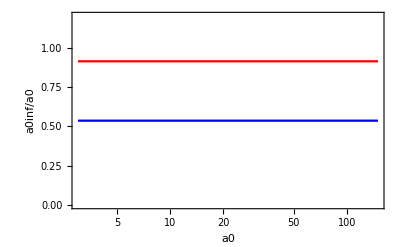

```mathematica
LogLinearPlot[{ ⅇ^(-xb^2/((1+(4 rb^2)/W0^2) (1+(8 rb^2)/W0^2) W0^2)) √((1+(4 rb^2)/W0^2)/(1+(8 rb^2)/W0^2))//.{W0->2,rb->0.5,xb->W0}, ⅇ^(-xb^2/((1+(4 rb^2)/W0^2) (1+(8 rb^2)/W0^2) W0^2)) √((1+(4 rb^2)/W0^2)/(1+(8 rb^2)/W0^2))//.{W0->2,rb->0.5,xb->0}},{a0,3,150},PlotRange->{0,1.2},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"a0","a0inf/a0"}]
```

## Figure 6

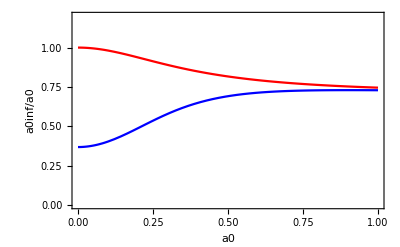

```mathematica
Plot[{ ⅇ^(-xb^2/((1+(4 rb^2)/W0^2) (1+(8 rb^2)/W0^2) W0^2)) √((1+(4 rb^2)/W0^2)/(1+(8 rb^2)/W0^2))//.{W0->2,xb->W0,rb->x W0}, ⅇ^(-xb^2/((1+(4 rb^2)/W0^2) (1+(8 rb^2)/W0^2) W0^2)) √((1+(4 rb^2)/W0^2)/(1+(8 rb^2)/W0^2))//.{W0->2,xb->0,rb->x W0}},{x,0,1},PlotRange->{0,1.2},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"a0","a0inf/a0"}]
```